## Training Data

```mathematica
Data2= Import["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/Accelerometer 123.csv","Data"];
```

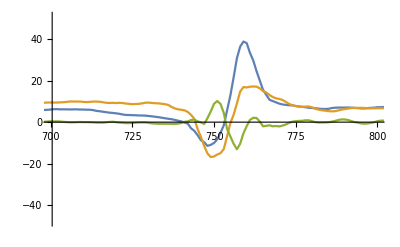

```mathematica
ListLinePlot[{Data2[[All,2]],Data2[[All,3]],Data2[[All,4]]},PlotRange-> {{700,800},Full}]
```

```mathematica
300*29+600
```

9300

```mathematica
p = Table[Part[Data2,n;;n+175],{n,675,9400,300}]
```

{{{6733,5.44328,8.21935,-0.313126},{6742,5.44328,8.20975,-0.351151},{6751,5.44328,8.34888,-0.303619},{6761,5.47678,8.35367,-0.265594},{6773,5.40981,8.37766,-0.127777},{6782,5.41458,8.33928,-0.0517426},{6791,5.38109,8.29131,-0.00419617},163,{8431,6.94081,7.1207,-0.251343},{8442,6.9073,7.1255,-0.246582},{8452,6.91689,7.05833,-0.208557},{8461,6.93602,7.02954,-0.118256},{8471,6.92166,6.948,-0.104019},{8482,6.89296,6.88562,-0.0944977}},28,{1}}
 |  |  |  |

```mathematica
gests = Monitor[Rasterize/@Table[ListLinePlot[{p[[n]][[All,2]],p[[n]][[All,3]],p[[n]][[All,4]]},PlotRange->All,Axes->None,AxesLabel->None,PlotStyle->{Red, Green, Blue}],{n,1,Length[p]}],n]
```

```mathematica
g1 = Table[Part[gests,1;;10][[x]]->1,{x,1,10}]
```

```mathematica
g2 = Table[Part[gests,11;;20][[x]]->2,{x,1,10}]
```

```mathematica
g3 = Table[Part[gests,21;;30][[x]]->3,{x,1,10}]
```

```mathematica
classifygestures = Join[g1,g2,g3]
```

```mathematica
gesturedata={-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3}
```

{-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3}

```mathematica
Gestures123 = Classify[gesturedata]
```

ClassifierFunction[…]

```mathematica
(*net=NetChain[{ConvolutionLayer[20,5],ElementwiseLayer[Ramp],PoolingLayer[2,2],ConvolutionLayer[50,5],ElementwiseLayer[Ramp],PoolingLayer[2,2],FlattenLayer[],LinearLayer[500],ElementwiseLayer[Ramp],LinearLayer[3],SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{"1","2","3"}}],"Input"->NetEncoder[{"Image",{360,223},"RGB"}]]*)
```

NetChain[<>]

```mathematica
net = NetModel["VGG-16 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
featureFunction=Take[net,{1,"fc7"}]
```

NetChain[<>]

```mathematica
training = Keys[gesturedata];
```

```mathematica
features=Map[featureFunction,training]
```

{{-1.87097,-1.65404,-0.0932931,3.11599,-1.34862,-1.0509,0.605974,4082,3.02791,-2.89978,-1.4934,0.161753,-3.41228,-2.13216,-0.787434},73,{1}}
 |  |  |  |

```mathematica
xyz = DimensionReduce[features,3,Method->"TSNE"];
Graphics3D[
MapThread[Inset[Thumbnail[RemoveBackground@#2,32],#1]&,{xyz,training}],
BoxRatios->{1, 1, 1}
]
```

-Graphics3D-

```mathematica
gestClassifier = Classify[gesturedata,FeatureExtractor->featureFunction]
```

ClassifierFunction[…]

```mathematica
n2=NetTrain[net,{-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3}]
```

NetChain[<>]

```mathematica
-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,
```

```mathematica
n2[-Graphics-,"Probabilities"]
```

<|1→0.00199383,2→0.989577,3→0.00842937|>

```mathematica
"3"
```

3

### Samples

```mathematica
gestClassifier/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
gestClassifier/@{ -Graphics-,-Graphics-,-Graphics-,-Graphics-}
gestClassifier/@{ -Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{1,1,1,1,1,1}

{2,2,2,2}

{3,3,3,3}

## Test Data

```mathematica
Data3= Import["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/3t.csv","Data"];
```

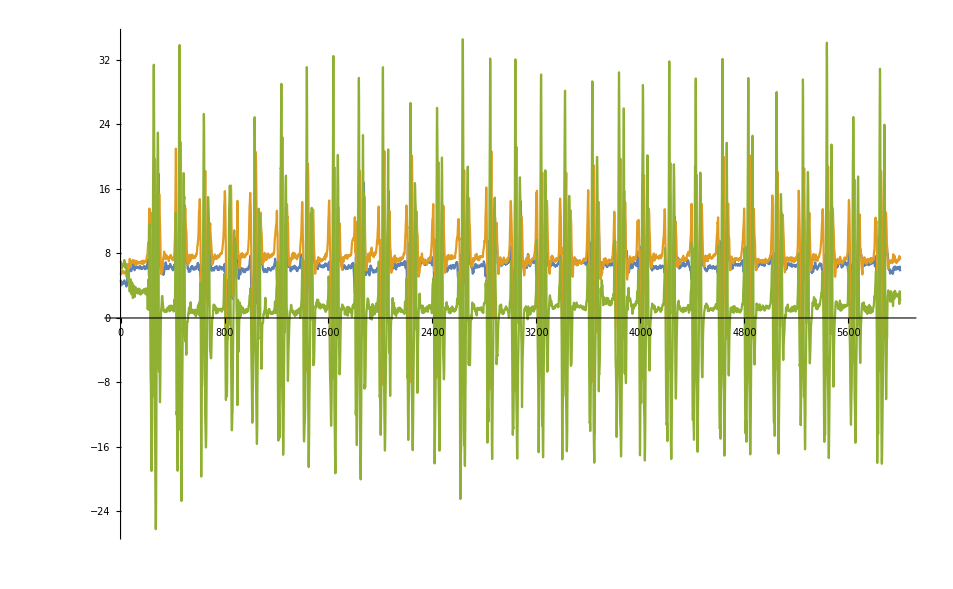

```mathematica
ListLinePlot[{Data3[[All,2]],Data3[[All,3]],Data3[[All,4]]},PlotRange->All]
```

```mathematica
300*29+600
```

9300

```mathematica
p2 = Table[Part[Data3,n;;n+175],{n,170,20*200+270,200}];
gests2 = Monitor[Rasterize/@Table[ListLinePlot[{p2[[n]][[All,2]],p2[[n]][[All,3]],p2[[n]][[All,4]]},PlotRange->All,Axes->None,AxesLabel->None,PlotStyle->{Red, Green, Blue}],{n,1,Length[p2]}],n]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
n2[-Graphics-]
```

3

```mathematica
g1 = Table[Part[gests2,1;;10][[x]]->3,{x,1,10}]
```

{-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3}

```mathematica
g2 = Table[Part[gests2,10;;Length[gests2]][[x]]->2,{x,10,Length[gests2]}]
```

Part::partw: Part 10 of … does not exist.

Part::partw: Part 11 of … does not exist.

Part::partw: Part 12 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
g3 = Table[Part[gests,21;;30][[x]]->3,{x,1,10}]
```

```mathematica
classifygestures = Join[g1,g2,g3]
```

```mathematica
Gestures123 = Classify[{-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3}]
```

ClassifierFunction[…]

```mathematica
net=NetChain[{FlattenLayer[],DotPlusLayer[3],SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{"1","2","3"}}],"Input"->NetEncoder[{"Image",{360,223},"RGB"}]]
```

NetChain[<>]

```mathematica
n2=NetTrain[net,{-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->3}]
```

NetChain[<>]

```mathematica
n2[-Graphics-]
```

2